Результаты по методу Эйлера с шагом h = 0.1

|  x |  y
 |  0.00000 |  0.00000
 |  0.10000 |  0.00000
 |  0.20000 |  0.00000
 |  0.30000 |  0.00000
 |  0.40000 |  0.00000
 |  0.50000 |  0.00000
 |  0.60000 |  0.00000
 |  0.70000 |  0.00000
 |  0.80000 |  0.00000
 |  0.90000 |  0.00000
 |  1.00000 |  0.00000

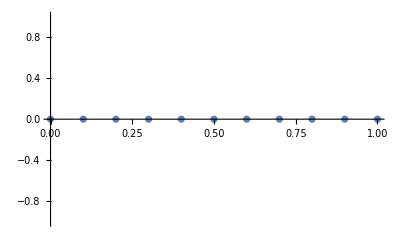

Результаты по методу Эйлера с шагом h = 0.1

```mathematica
(*исходные данные*)
f[x_,y_] := y*(x*y-2)/2*x;
a = 1;
b = 2;
y0 = 0.;
x0 =0.;
h = 0.1;
m = Floor[(b-a)/h] +1;

(*расчет по методу Эйлера*)
x = x0;
y = y0;
eu1 = Table[{x,y} = {x+h,y+h*f[x,y]},{i,m -1}];
eu1 = Prepend[eu1,{x0,y0}];

Print["Результаты по методу Эйлера с шагом h = 0.1"];
gr1 := ListPlot[eu1];

lst = {{},{" x"," y"}};
PaddedForm[TableForm[eu1,TableHeadings->lst],{5,5}]
Show[{gr1,gr2}]

(*для контроля сравним полученный результат с точным решением*)
g[x_] := 2/(x*(1-Log[x]))

gr2 := Plot[g[x],{x,a,b}]
"Результаты по методу Эйлера с шагом h = 0.1"
```